```mathematica
f1[x_]=(Sin[x])^3*Cos[x]+Cos[-8x];
f2[x_]=(x^5+x^4)*Log[x];
f3[x_]=Exp[b*x]*(c1*Sin[x]+c2*Cos[x]);
f4[x_]=Sin[a*x]*Cos[b*x]
f5[x_]=Exp[4x+3]*(x^2+x)
Integrate[f5[x],x]
```

Cos[b x] Sin[a x]

ⅇ^(3+4 x) (x+x^2)

1/32 ⅇ^(3+4 x) (-1+4 x+8 x^2)

```mathematica
list=RandomInteger[{-10,10},2];
p[x_]=AlgebraicNumber[x,list] (*random polynomial*)
Integrate[Exp[a*x]*p[x],x]
Integrate[Sin[a*x]*p[x],x]
Integrate[Cos[a*x]*p[x],x]
Integrate[Sin[a*x]*Exp[b*x]*p[x],x]
```

-9-9 x

-(9 ⅇ^(a x) (-1+a+a x))/a^2

(9 Cos[a x])/a+(9 x Cos[a x])/a-(9 Sin[a x])/a^2

-(9 Cos[a x])/a^2-(9 Sin[a x])/a-(9 x Sin[a x])/a

-(9 ⅇ^(b x) (-a (a^2 (1+x)+b (-2+b+b x)) Cos[a x]+(b^2 (-1+b+b x)+a^2 (1+b+b x)) Sin[a x]))/((a^2+b^2)^2)

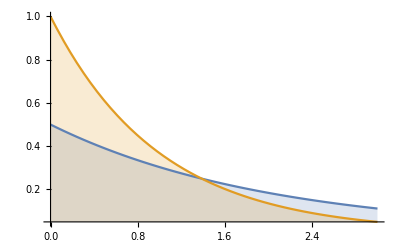

2 ⅇ^(-2 x)

1

1/2

1/2

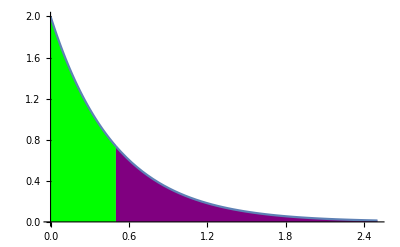

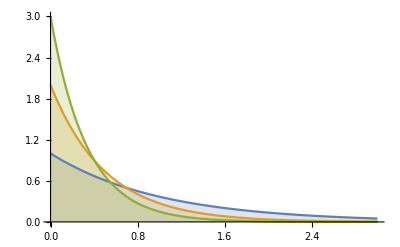

```mathematica
Plot[Table[PDF[ExponentialDistribution[λ],x],{λ,{0.5,1}}]//Evaluate,{x,0,3},Filling->Axis,PlotRange->Full]
λ=2;p[x_]=λ*Exp[-λ*x] (*exponential distribution*)
Integrate[p[x],{x,0,Infinity}]                
μ=Integrate[x*p[x],{x,0,Infinity}]  (*mean*)
σ=Sqrt[Integrate[(x-μ)^2*p[x],{x,0,Infinity}]] (*standard deviation*)
xMax=5*μ;
p1=Plot[p[x],{x,0,μ},Filling->Axis,FillingStyle->Green,PlotRange->{{0,μ},{0,3}}];
p2=Plot[p[x],{x,μ,xMax},Filling->Axis,FillingStyle->Purple];
Show[p1,p2,PlotRange->Full]
```